```mathematica
(* after running visio.nb run Init data, rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ], Error Estimation*)
```

### Init data

```mathematica
ρ0=1;
L1=Lx;
L2=Ly;
γ=1.4;
c=1.4;
eps=0.000001;
alphaa=2;
timeP = 2.0;
initrho[r_]:=eps Exp[-alphaa r^2]
```

```mathematica
NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]
```

NIntegrate::inumr: The integrand initrho[x,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4},{0,4}}.

NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]

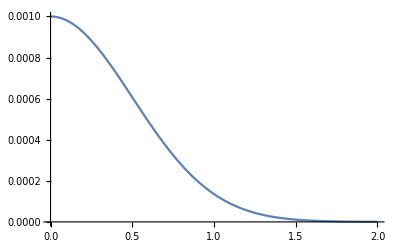

```mathematica
Plot[initrho[r],{r,0,2}]
```

### Analytical solutions for density, velocity, pressure, energy

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=eps/(2alphaa)NIntegrate[Exp[-ξ^2/(4alphaa)]Cos[ξ t]BesselJ[0,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞},Method->{Automatic,"SymbolicProcessing"->False},WorkingPrecision->15 ,MaxPoints->500]
```

```mathematica
uAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(x-L1/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
vAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(y-L2/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
mcrCenterLine=MeshCellRcm[[nx ny/2+1;;nx ny/2+nx]];
```

```mathematica
mmm=Table[MeshCellRcm[[i]],{i,MeshCellRcm//Length}];
```

```mathematica
rhoAn[mmm[[1,1]],mmm[[1,2]],2.0]
```

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 2.05202×10^-10 and 1.4803×10^-7 for the integral and error estimates.

5.13005×10^-17

### Center values for graphics

```mathematica
dataAnCenterRhoEqP=ParallelTable[{mmm[[i,1]],rhoAn[mmm[[i,1]],mmm[[i,2]],timeP]+1},{i,mcrCenterLine//Length}];
dataAnCenterU=ParallelTable[{mmm[[i,1]],uAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
dataAnCenterV=ParallelTable[{mmm[[i,1]],vAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
```

```mathematica
dataAnCenterE=Transpose@{dataAnCenterRhoEqP[[All,1]],dataAnCenterRhoEqP[[All,2]]/(γ-1)+1/2 dataAnCenterRhoEqP[[All,2]](dataAnCenterU[[All,2]]*dataAnCenterU[[All,2]] + dataAnCenterV[[All,2]]*dataAnCenterV[[All,2]])};
```

```mathematica
dataAnCenterH=Transpose@{dataAnCenterRhoEqP[[All,1]],1/dataAnCenterRhoEqP[[All,2]](dataAnCenterE[[All,2]] + dataAnCenterRhoEqP[[All,2]])};
```

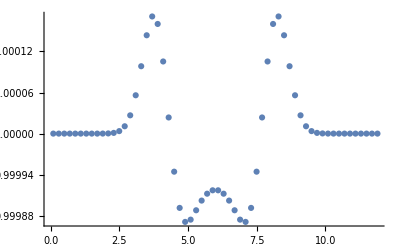

```mathematica
dataExact=ListPlot[dataAnCenterRhoEqP,PlotRange->All]
```

### Error Estimation

```mathematica
cellQuarter=Flatten[Table[MeshCellRcm[[i*nx+j]],{i,0,0.5ny-1},{j,1,0.5nx}],1];
```

```mathematica
cellNodes=Table[{
{cellQuarter[[i,1]]-hx/2,cellQuarter[[i,2]]-hy/2},
{cellQuarter[[i,1]]+hx/2,cellQuarter[[i,2]]-hy/2},
{cellQuarter[[i,1]]+hx/2,cellQuarter[[i,2]]+hy/2},
{cellQuarter[[i,1]]-hx/2,cellQuarter[[i,2]]+hy/2}},
{i,cellQuarter//Length}];
```

```mathematica
cells=Table[Polygon[cellNodes[[i]]],{i,1,cellNodes//Length}];
cells[[1]]
```

Polygon[{{0.,0.},{0.4,0.},{0.4,0.4},{0.,0.4}}]

```mathematica
Clear[cellNodes]
```

```mathematica
fDiffer[x_,y_,t_,n_]:=Abs[rhoAn[x,y,t]-GetSol[alpha,n,1,{x,y}]+1]
```

#### NormC

```mathematica
NMaxValue[{fDiffer[x,y,timeP,45],{x,y}∈cells[[45]]},{x,y}]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

6.47364×10^-8

```mathematica
6.473642428272352*^-8
```

```mathematica
maxitable=ParallelTable[NMaxValue[{fDiffer[x,y,timeP,n],{x,y}∈cells[[n]]},{x,y}],{n,1,cellNodes//Length}];
maxitable[[1]]
```

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 6.12034618456019×10^-11 and 1.7226844454351×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.000538464723587461 and 3.98317010802724×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 3.44135001372037×10^-10 and 1.91642885909237×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00210311927860111 and 4.24378537667312×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 7.56597330141355×10^-10 and 1.50647017320837×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00330481299210049 and 3.59885727963904×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00615745813924563 and 2.31843166693608×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00649157344309698 and 2.09843932434643×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00669426419197699 and 1.92493575850326×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 1.07773656693432×10^-6 and 6.60985405278894×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 3.06170223273793×10^-6 and 2.58135429644919×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 5.21112412674518×10^-6 and 2.95453058732058×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.0000106931189033536 and 4.35037461889909×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.0000248567212829791 and 4.82118727944019×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.0000391827798804326 and 4.82400773987206×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00472710133403168 and 2.87395702012873×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00673810239189537 and 1.88839737598506×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00495437728222941 and 2.76978425696997×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.000294885663049394 and 3.28758165810362×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00047908594201494 and 3.90015735011734×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.000658628464197909 and 3.9624321201539×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.0000686943857918722 and 2.93703596614691×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.000132523485663823 and 3.48308047080021×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.000873643974753804 and 2.89608451097875×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.000194519880426338 and 2.86012976719311×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.001212219134571 and 2.87705711807194×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00157015357630244 and 3.87083169963284×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaxValue::cvmit will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaxValue::cvmit will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00184173528557362 and 3.18960176094406×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00220885565531286 and 4.1920314796246×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00271049385656482 and 2.85834359114593×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00283387652667873 and 2.67169817696787×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00296230524923126 and 2.97242202241222×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 0.00345897943791055 and 3.51503048402698×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1.53807×10^-11

```mathematica
Max[maxitable]
```

```mathematica
7.013088385304251*^-7
```

```mathematica
7.013088385292531*^-7
```

```mathematica
3.8120223137315363*^-7
```

```mathematica
8.112305699191237*^-8
```

```mathematica
8.112305487071103*^-8
```

```mathematica
4.5730865555452755*^-8
```

```mathematica
5.6039898640702734*^-8
```

```mathematica
1.4663909406483854*^-7
```

```mathematica
3.49980129889861*^-8
```

#### Norm L1

```mathematica
NIntegrate[fDiffer[x,y,timeP,1],{x,y}∈cells[[1]],
WorkingPrecision->15 ,MaxPoints->2000]
```

1.0819717280141×10^-12

```mathematica
intable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n],{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ,MaxPoints->2000],{n,1,cellNodes//Length}];
intable[[1]]
```

1.0819717280141×10^-12

```mathematica
Sum[intable[[i]],{i,intable//Length}]
```

```mathematica
1.84373535687566433811947021850147`15.*^-6
```

```mathematica
1.09375198280445717852985841435017`15.*^-6
```

```mathematica
4.2946188445809258019148826416134`15.*^-7
```

```mathematica
1.39303387530596154344121589865928`15.*^-6
```

```mathematica
1.39680162709597125420651450137597`15.*^-6
```

```mathematica
1.39816238190462637371729712980992`5.*^-6
```

```mathematica
4.4620311025502396 ^-7
```

#### Norm L2

```mathematica
(*надо переделать - квадрат возмущения считают по всей расчетной области*)
```

```mathematica
insqrtable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n]^2,{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ,MaxPoints->2000],{n,1,cellNodes//Length}];
insqrtable[[1]]
```

9.42122560599295×10^-24

```mathematica
√Sum[insqrtable[[i]],{i,insqrtable//Length}]
```

```mathematica
8.0061403970885980209334252486821`15.301029995663974*^-7
```

```mathematica
4.4030290576288594175615632742439`15.301029995663981*^-7
```

```mathematica
8.097684201245305212998232964007`15.301029995663962*^-8
```

```mathematica
2.4485155921685051401437828656416`15.301029995663969*^-7
```

```mathematica
8.295058830784622 ^-8
```